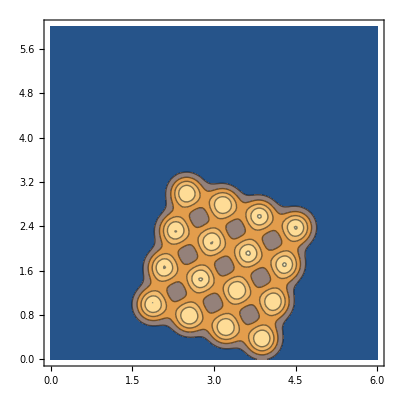

```mathematica
xs =ys=0.3;
t=0.3;
μx1=μy1=0.7;
μx2=μy2=1.5;
ContourPlot[Sum[Exp[-(((x) Cos[t]-(y) Sin[t]-j μx1-μx2)/xs)^2-(((y) Cos[t]+(x)Sin[t]-i μy1-μy2)/ys)^2],{i,0,3},{j,0,3}],{x,0,6},{y,0,6},PlotRange->All,PerformanceGoal->"Quality"]
```

```mathematica
Clear[xs,ys,t,μx1,μy1,μx2,μy2]
Solve[{((x) Cos[t]-(y) Sin[t]-j μx1-μx2)/xs==0,((y) Cos[t]+(x)Sin[t]-i μy1-μy2)/ys==0},{x,y},Reals]
```

{{x→ConditionalExpression[Csc[t] (i μy1+μy2-(Cos[t] (i μy1 Cos[t]+μy2 Cos[t]-j μx1 Sin[t]-μx2 Sin[t]))/(Cos[t]^2+Sin[t]^2)),(xs>0&&ys>0)||(xs>0&&ys<0)||(xs<0&&ys>0)||(xs<0&&ys<0)],y→ConditionalExpression[(i μy1 Cos[t]+μy2 Cos[t]-j μx1 Sin[t]-μx2 Sin[t])/(Cos[t]^2+Sin[t]^2),(xs>0&&ys>0)||(xs>0&&ys<0)||(xs<0&&ys>0)||(xs<0&&ys<0)]}}

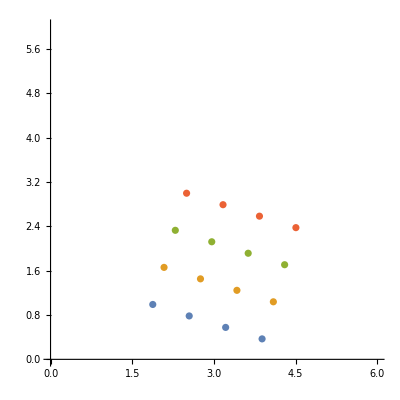

```mathematica
xs =ys=0.3;
t=0.3;
μx1=μy1=0.7;
μx2=μy2=1.5;
ListPlot[Table[{Csc[t] (i μy1+μy2-(Cos[t] (i μy1 Cos[t]+μy2 Cos[t]-j μx1 Sin[t]-μx2 Sin[t]))/(Cos[t]^2+Sin[t]^2)),(i μy1 Cos[t]+μy2 Cos[t]-j μx1 Sin[t]-μx2 Sin[t])/(Cos[t]^2+Sin[t]^2)},{i,0,3},{j,0,3}],PlotRange->{{0,6},{0,6}},AspectRatio->1]
```

```mathematica
({{Cos[t], -Sin[t]}, {Sin[t], Cos[t]}}).({{x}, {y}})
```

{{x Cos[t]-y Sin[t]},{y Cos[t]+x Sin[t]}}

```mathematica
Clear[xs,ys,t]
```

```mathematica
Collect[-(((x) Cos[t]-(y) Sin[t]-j μx1-μx2)/xs)^2-(((y) Cos[t]+(x)Sin[t]-i μy1-μy2)/ys)^2//Expand,x]
```

-(j^2 μx1^2)/xs^2-(2 j μx1 μx2)/xs^2-μx2^2/xs^2-(i^2 μy1^2)/ys^2-(2 i μy1 μy2)/ys^2-μy2^2/ys^2+(2 i y μy1 Cos[t])/ys^2+(2 y μy2 Cos[t])/ys^2-(y^2 Cos[t]^2)/ys^2-(2 j y μx1 Sin[t])/xs^2-(2 y μx2 Sin[t])/xs^2-(y^2 Sin[t]^2)/xs^2+x ((2 j μx1 Cos[t])/xs^2+(2 μx2 Cos[t])/xs^2+(2 i μy1 Sin[t])/ys^2+(2 μy2 Sin[t])/ys^2+(2 y Cos[t] Sin[t])/xs^2-(2 y Cos[t] Sin[t])/ys^2)+x^2 (-Cos[t]^2/xs^2-Sin[t]^2/ys^2)